## Notes

>>>Note the code belows derives from internal version: grf_c_graphs_alzheimer’s_4.nb
>>> This code is used to display the results from the classification model.
>>> The graphs are also used as a guide for mapping classing so that different runs can be summed
>>> By looking at the topology of the graph it is possible to see the corresponding clusters. 
>>> The classes can then be used to do the mapping in the classification model notebook.

## Data Loading

```mathematica
SetDirectory["/Users/jeffreylapides/Documents/Mathematica_new/alzheimers"];
```

>>> Load data to be graphed. See example of file format below. 
>>> index, three top classes connected by colons, class components
>>> code below will create a graph of this data

```mathematica
dt1Output=Import["Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.15rrtst_docTopicSum.csv"];
Length@%
```

122

```mathematica
dt1Output[[1]]
```

{1,2:1:5,0.296703,0.48489,0.00412088,0.00412088,0.210165}

>>> this file is very important to keep various files registered/aligned properly as the classification model
>>> could filter out some samples. This file has the original indices to keep track of what made it into the results >>> file. If the results from the classification model are in memory, you don’t have to load this file. This file is 
>>> stored in the export section so you can always start with the graph code and just reload it.
>>> use if not loaded from topic model.

```mathematica
dataIX=Flatten[Import["Alzheimers_AK_5_topics_a_0P3_b_0P25_cut_1_12.15rrtst1_dataIX.csv"]];
Length@%
```

122

```mathematica
dataIX
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123}

>>> Code for tooltips

```mathematica
doctopics3=dt1Output;
Length@%
tk1=ToExpression[Import["microbiome_alzheimer's_input_11_s1.tsv","TSV"]];
Length@%
tk2={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@Import["microbiome_alzheimer's_input_11a_s1.tsv","TSV"];
Length@%
datatest=tk1;
Length@dataIX
Do[tksampTdata[tk2[[i,2]]]=tk2[[i,3]],{i,1,Length[tk2]}]
```

122

123

123

122

>>> METADATA is loaded in the classification model. If not loaded there load here.

```mathematica
md1=Import["md1UAMS.csv", "CSV"];
```

>>> HERE If not loaded in classification model, do this:
>>> used for tool tips in graphs

```mathematica
tk1graph=tk1;
```

## Functions

>>>Note assumes dist input,need to parameterize for distR01,etc.,or force the situation

```mathematica
distmeas[sample_,cutoff_, ioracc_Integer]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal},
dist = Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],comp1[[sample[[i]],2]].comp1[[sample[[j]],2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],0}],{i,1,Length@comp1},{j,1,Length@comp1}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]>cutoff&];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd];
distfinal = If[ioracc==0,distfd, distfds];
distfinal
]

distmeas1[sample_,cutoff_, ioracc_Integer,t_]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal},
dist = Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],trunc[comp1[[sample[[i]],2]],t].trunc[comp1[[sample[[j]],2]],t]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],0}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]>cutoff&];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd];
distfinal = If[ioracc==0,distfd, distfds];
distfinal
]

distmeasEu[sample_,cutoff1_, cutoff2_,oppnets_,ioracc_Integer]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal,ONdistn},
(*cutoff1 is for top three topics. Cutoff 2 is for all topics*)
topThreeIX=Table[ToExpression[StringSplit[doctopics3[[sample[[i]],23]],":"]],{i,1,Length[sample]}];
topThreeComp=Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]], Sqrt[Total[(comp1[[sample[[i]],2]][[topThreeIX[[i]]]]-comp1[[sample[[j]],2]][[topThreeIX[[i]]]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
dist = Table[If[i<j&&topThreeComp[[i,j,3]]<cutoff1,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],Sqrt[Total[(comp1[[sample[[i]],2]]-comp1[[sample[[j]],2]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]<cutoff2&];
(*Find distances of OppNets to all, then look at ten with smallest distance*)
ONdist=Table[SortBy[Select[distfd,#[[1]]==oppnets[[i]]||#[[2]]==oppnets[[i]]&],Last],{i,1,Length[oppnets]}];
ONdist1=Table[Take[ONdist[[i]],If[Length[ONdist[[i]]]≥10,10,Length[ONdist[[i]]]]],{i,1,Length[oppnets]}];
(*Find non-OppNet Grants related to each OppNet {output grant ID, ApplID, Title, distance}*)
nonON = Table[Table[Flatten[{Complement[{ONdist1[[i,j,1]],ONdist1[[i,j,2]]},{oppnets[[i]]}],ONdist1[[i,j,3]]},1],{j,1,Length[ONdist1[[i]]]}],{i,1,Length[oppnets]}];
(*Create non-OppNet Lists WITH IX, ApplID, Tittle, distance based on Oppnets*)
lists0=Map[Style[StringJoin[ToString[doctopics3[[#,1]]],"-",ToString[doctopics3[[#,2]]],"-",doctopics3[[#,8]],"-",doctopics3[[#,19]]],Bold]&,oppnets];
lists1=Map[StringJoin[ToString[doctopics3[[#[[1]],1]]],"-",ToString[doctopics3[[#[[1]],2]]],"-",doctopics3[[#[[1]],8]],"-",doctopics3[[#[[1]],19]],"-",ToString[#[[2]]]]&,nonON,{2}];
lists2=If[Length[lists1]==Length[lists0],Table[Flatten[{lists0[[i]],lists1[[i]]}],{i,1,Length[lists0]}],{}];
distfd1=Map[{#[[1]],#[[2]],1/#[[3]]}&,distfd];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd1];
distfinal = If[ioracc==0,distfd1, distfds];
distfinal
]
distmeasEu1[sample_,cutoff1_, cutoff2_,ioracc_Integer]:=Module[{distTst,distf,distfj,distff,distfs,distfd,distfds,distfinal,ONdistn},
(*cutoff1 is for top three topics. Cutoff 2 is for all topics*)
topThreeIX=Table[ToExpression[StringSplit[doctopics3[[sample[[i]],topTopicsPos]],":"]],{i,1,Length[sample]}];
topThreeComp=Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]], Sqrt[Total[(comp1[[sample[[i]],2]][[topThreeIX[[i]]]]-comp1[[sample[[j]],2]][[topThreeIX[[i]]]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
dist = Table[If[i<j&&topThreeComp[[i,j,3]]<cutoff1,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],Sqrt[Total[(comp1[[sample[[i]],2]]-comp1[[sample[[j]],2]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]<cutoff2&];
distfd1=Map[{#[[1]],#[[2]],If[#[[3]]≠0.,1/#[[3]],99]}&,distfd];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd1];
distfinal = If[ioracc==0,distfd1, distfds];
distfinal
]
dist=distR01;
distcutoff[histCutoff_,distCutoff_,binWidth_]:=Module[{t,y,sing1},
sing={};
(*dist=distR01;*)
bc=Table[BinCounts[Map[#[[3]]&,dist[[t,y]]],binWidth],{t,1,25},{y,1,9}];
bcacc=Table[Accumulate[N[bc[[t,y]]/(If[Total[bc[[t,y]]]<1,AppendTo[sing,ToString[t]<>"-"<>ToString[y]];100+Total[bc[[t,y]]],Total[bc[[t,y]]]])]],{t,1,25},{y,1,9}];
bcaccix=Table[{i,bcacc[[t,y,i]]},{t,1,25},{y,1,9},{i,1,Length[bcacc[[t,y]]]}];
cutoff=Table[(Min[If[Select[bcaccix[[t,y]],#[[2]]>histCutoff&]=={},0,Map[#[[1]]&,Select[bcaccix[[t,y]],#[[2]]>histCutoff&]]]]*binWidth+distCutoff),{t,1,25},{y,1,9}];
cutoff
]
graphlabel=Table["Topic - "<>ToString[k]<>" - "<>ToString[2008-1+j],{k,1,25},{j,1,9}];
graphlabelR01=Table["R01 - Topic - "<>ToString[k]<>" - "<>ToString[2008-1+j],{k,1,25},{j,1,9}];
grfb[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,graphlabel_,vSpec_Integer]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
(*vertices2 =  Table[Tooltip[vertices[[i]],"Acc# - "<>ToString[IXapplIDNEWassoc[[Key[vertices[[i]]]]]]<>", State: "<>doctopics3[[vertices[[i]],20]]<>", Top Topics #: "<>"N/A"<>", \nTitle: "<>doctopics3[[vertices[[i]],8]]<>",\n"<>"Top Keywords: "<>"N/A"<>", RCDC: N/A"<>(*doctopics3[[vertices[[i]],8]]),*) ", Award: $"<>ToString[doctopics3[[vertices[[i]],14]]]<>",  Start-Year: "<>ToString[doctopics3[[vertices[[i]],7]]]],{i,1,Length[vertices]}];*)
(*inst={"MH","AA","DA","AG","HD","NS", "DC"};
instCode=Map[If[Or@@Table[#[[9]]==inst[[k]],{k,1,7}],Switch[#[[9]],"MH",Red,"AA",Blue, "DA",Yellow, "AG",Green, "HD",Magenta,"NS",Orange,"DC",Cyan],Gray]&,doctopics3];*)
inst={"AA","AG","CA","DA",  "HD", "HL","MH"};
instCode=Map[If[Or@@Table[#[[9]]==inst[[k]],{k,1,7}],Switch[#[[9]],"MH",Red,"AA",Blue, "DA",Yellow, "AG",Green, "HD",Magenta,"HL",Orange,"CA",Cyan],Gray]&,doctopics3];
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
grf=Graph[vertices,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,
VertexStyle->Table[vertices[[i]]->instCode[[vertices[[i]]]],{i,1,Length[vertices]}],
VertexLabels->If[lblflg==1,Table[vertices[[i]]->Style[doctopics3[[vertices[[i]],23]],8],{i,1,Length[vertices]}],None],
(*VertexStyle->Table[vertices[[i]]->ccstyle[[i]],{i,1,Length[vertices]}],VertexSize->{931->{0.1,0.2}},*)PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
grfTopics1[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,graphlabel_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCode},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],10];
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,10}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Yellow, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
verticesLBL={#[[1]],#[[2]]}&/@Map[doctopics3[[#]]&,vertices];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL[[j]]],{j,1,Length[vertices]}];
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->4,#[[1]]->2]&,bacYesNo];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],
PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
```

```mathematica
grfTopics2old[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,graphlabel_,vtex_,cond_, rfp_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCodeHld},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
(*The next line assigns color by highest to lowest occurring class*)
(*tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];*)
(*The next line assigns color by class number*)
tentopics=ToString[#]&/@Range[tnum];
(*not sure what next line is*)
(*tentopics=Join[tentopics,Range[tnum+1,10]];*)
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Yellow, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
colx=Gray;
(*topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],colx,tentopics[[2]],colx,tentopics[[3]],colx, tentopics[[4]],colx,tentopics[[5]],colx,tentopics[[6]],colx,tentopics[[7]],colx,tentopics[[8]],colx,tentopics[[9]],colx,tentopics[[10]],colx],colx]&,doctopics3];*)
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
verticesLBL={#[[1]],#[[2]],#[[3;;]]}&/@Map[doctopics3[[#]]&,vertices];
verticesLBL1=#[[2]]&/@Map[tk1[[#]]&,vertices];
verticesLBL1a=#[[2]]&/@Map[tk1graph[[#]]&,vertices];
verticesLBL2=Map[{md1[[#]], dataIX[[#]]}&,vertices];
verticesLBL3=Map[allTable2[[#]]&,vertices];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL3[[j]]],{j,1,Length[vertices]}](*version 2*);
verticesTT=Table[Tooltip[vertices[[j]],{verticesLBL[[j]],verticesLBL1[[j]],verticesLBL1a[[j]],verticesLBL2[[j]]}],{j,1,Length[vertices]}](*version 1*);
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->1]&,bacYesNo];
If[Length[vtex]>0,Goto[many]];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->3,#[[1]]->#[[2]]]&,vertexSize];
vertexSize=If[ToString[Head[vtex]]=="String",Map[If[StringTake[#[[4,allTabPos1]],2]==vtex,#[[1]]->2,#[[1]]->1]&,Map[allTable2[[#]]&,vertices]],vertexSize];
Label[many];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->1.5,#]&,vertexSize],vertexSize];
(*vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->2]&,bacYesNo];*)
diseaseShape1=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1]],#[[4,2]]}&,Map[allTable2[[#]]&,vertices]],#[[2]]==cond&]];
diseaseShape11=Map[#[[1]]->If[#[[1]]≥133,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
diseaseShape11=Map[#[[1]]->If[#[[4,allTabPos]]==cond,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape1,EdgeStyle->Lighter[Gray,0.25],PlotLabel->Style[graphlabel,18,Black,Bold]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape11,EdgeStyle->Lighter[Gray,0.25],PlotLabel->Style[graphlabel,14,Black,Bold]];
grf
]
```

>>>graph_code - CURRENT VERSION IN USE

```mathematica
grfTopics2[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,graphlabel_,vtex_,cond_, rfp_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCodeHld},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]≠0&&#[[3]]<cutoffU&];
edgeWeights=If[#[[3]]≥0.5,50,1]&/@edges;
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
Do[ixdataIX[dataIX[[i]]]=i,{i,1,Length@dataIX}];
(*The next line assigns color by highest to lowest occurring class*)
(*tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];*)
(*The next line assigns color by class number*)
tentopics=ToString[#]&/@Range[tnum];
(*not sure what next line is*)
(*tentopics=Join[tentopics,Range[tnum+1,10]];*)
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Orange, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Yellow,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3[[#]]&/@vertices];
colx=Gray;
(*topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],colx,tentopics[[2]],colx,tentopics[[3]],colx, tentopics[[4]],colx,tentopics[[5]],colx,tentopics[[6]],colx,tentopics[[7]],colx,tentopics[[8]],colx,tentopics[[9]],colx,tentopics[[10]],colx],colx]&,doctopics3];*)
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
verticesLBL={#[[1]],#[[2]],#[[3;;]]}&/@(doctopics3[[#]]&/@vertices);
verticesLBL1=#[[2]]&/@Map[tk1[[#]]&,dataIX[[#]]&/@vertices];
verticesLBL1a=#[[2]]&/@Map[tk1graph[[#]]&,dataIX[[#]]&/@vertices];
verticesLBL2=Map[{md1[[#]],tk2[[#,2]],tk2[[#,1]],subjIX[md1[[#,8]]]}&,dataIX[[#]]&/@vertices];
(*verticesLBL3=Map[allTable2[[#]]&,(ixdoctopics3[#]&/@vertices) ];*)
(*verticesTT=Table[Tooltip[vertices[[j]],verticesLBL3[[j]]],{j,1,Length[vertices]}]*)(*version 2*);
verticesTT=Table[Tooltip[vertices[[j]],{verticesLBL[[j]],verticesLBL1[[j]],verticesLBL1a[[j]],verticesLBL2[[j]]}],{j,1,Length[vertices]}](*version 1*);
bacYesNo=Map[{ixdataIX[#[[1]]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];
(*bacYesNo=Map[{ixdataIX[#[[1]]],And@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];*)
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->1]&,bacYesNo];
If[Length[vtex]>0,Goto[many]];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->3,#[[1]]->#[[2]]]&,vertexSize];
vertexSize=If[ToString[Head[vtex]]=="String",Map[If[StringTake[#[[4,allTabPos1]],2]==vtex,#[[1]]->2,#[[1]]->1]&,Map[allTable2[[#]]&,vertices]],vertexSize];
Label[many];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->1.5,#]&,vertexSize],vertexSize];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->2.1,#]&,vertexSize],vertexSize];
(*vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->2]&,bacYesNo];*)
(*diseaseShape1=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1]],#[[4,2]]}&,Map[allTable2[[#]]&,vertices]],#[[2]]==cond&]];
diseaseShape11=Map[#[[1]]->If[#[[1]]≥133,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];*)
diseaseShape11=Map[#[[1]]->If[#[[4,allTabPos]]==cond,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp,"EdgeWeighted"->True},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[i]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape11,EdgeStyle->Lighter[Gray,0.25],EdgeWeight->edgeWeights, PlotLabel->Style[graphlabel,14,Black,Bold]];
grf
]
```

```mathematica
Do[ixdoctopics3[doctopics3[[i,1]]]=i,{i,1,Length@doctopics3}]
```

```mathematica
Do[ixtk1graph[tk1graph[[i,1]]]=i,{i,1,Length@tk1graph}]
```

```mathematica
Do[ixallTable[allTable[[i,1,1]]]=i,{i,1,Length@allTable}]
```

```mathematica
Do[ixdataIX[dataIX[[i]]]=i,{i,1,Length@dataIX}]
```

```mathematica
ixdataIX[153]
```

ixdataIX[153]

```mathematica
grfTopics3[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,cond_,graphlabel_,vtex_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopicsn,topicCode,vLength,rand},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
(*vLength=Length[vertices];
rand=RandomReal[{0,1},vLength];
vertices=#[[1]]&/@SortBy[Map[{vertices[[#]],rand[[#]]}&,Range[1,vLength]],Last];*)
vlist=vertices; (*for output*)
tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[{#[[1]],#[[2]]}&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];
tentopics=Join[tentopics,Range[tnum+1,10]];
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,10}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Blue,tentopics[[2]],Red,tentopics[[3]],Magenta, tentopics[[4]],Yellow,tentopics[[5]],Green,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
(*Edit, remove next line after I ge the +1 fixed in subsequent lines*)
(*tsts=metadata[[subjidTixmetadata[tkixTname[vertices[[i]]]]+1]];*)
metaIX=Table[If[ToString[Head[subjidTixmetadata[If[Head[tkixTname[vertices[[i]]]]==String,tkixTname[vertices[[i]]],"XXX"]]]]=="Integer",subjidTixmetadata[If[Head[tkixTname[vertices[[i]]]]==String,tkixTname[vertices[[i]]],"XXX"]],"NA"],{i,1,Length@vertices}];
condition=Map[If[metaIX[[#]]≠"NA", ToString[metadata[[metaIX[[#]]+1,3]]],"NA"]&,Range[1,Length[metaIX]]];
(*Edit*)
(*verticesLBL0={#[[1]],#[[2]]}&/@Map[doctopics3[[#]]&,vertices];*)
(*position of components needs to be parametered, posComp doesn't do it*)
verticesLBL0={#[[1,1]],#[[1,2]],#[[1,3]],#[[1,6;;10]],#[[2]]}&/@Map[doctopics5[[#]]&,vertices];
(*doctopics5 is not in vertex order next line is a problem*)
(*verticesLBL=Map[Join[verticesLBL0[[#]],{condition[[#]]},doctopics5[[#,3]]]&,Range[1,Length[vertices]]];*)
verticesLBL=Map[Join[verticesLBL0[[#]],{condition[[#]]}]&,Range[1,Length[vertices]]];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL[[j]]],{j,1,Length[vertices]}];
(*Eventually change to doctopics5 from tk2*)
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[3]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk2[[#]]&,vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
(*diseaseShape=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1,1]],#[[1,5]]}&,Map[doctopics5[[#]]&,vertices]],#[[2]]==cond&]];*)
diseaseShape=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1,1]],#[[1,5]]}&,Map[doctopics5[[#]]&,vertices]],IntersectingQ[StringSplit[#[[2]],":"],{cond}]&]];
vertexSize=Map[If[#[[2]]==True,#[[1]]->3.0,#[[1]]->1.5]&,bacYesNo];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->6,#[[1]]->#[[2]]]&,vertexSize];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape,PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
```

## Graphs

### Graph Setup

>>> These are variables use to compute node similarity below and also used in node tooltips
>>> The graph below shows the total of all the components by class.

{7503,27.0468,26.4891,23.5714,20.5278,24.3649}

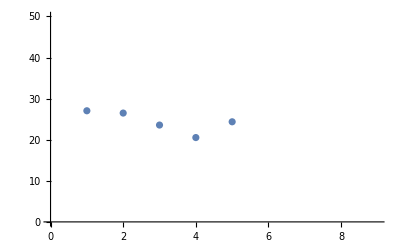

```mathematica
posComps=3;
numTopics=topicnum;
topTopicsPos=2;
applIDIXNEWassoc=Association[Map[#[[2]]->#[[1]]&,doctopics3]];
IXapplIDNEWassoc=Association[Map[#[[1]]->#[[2]]&,doctopics3]];
comp=Map[Catenate[{{#[[1]]},Table[#[[i-1+posComps]],{i,1,numTopics}]}]&,doctopics3];
comp1=Table[{comp[[i,1]],Take[comp[[i]],-(Length[comp[[1]]]-1)]},{i,1,Length[comp]}];
compTotal=Total[comp]
ListPlot[compTotal[[2;;numTopics+1]],PlotRange->{{0,9},{0,50}}]
```

>>> This histogram shows the occurrence of component values for the whole data set within logarithmic bins.

{0.001,0.00112202,0.00125893,0.00141254,0.00158489,0.00177828,0.00199526,0.00223872,0.00251189,0.00281838,0.00316228,0.00354813,0.00398107,0.00446684,0.00501187,0.00562341,0.00630957,0.00707946,0.00794328,0.00891251,0.01,0.0112202,0.0125893,0.0141254,0.0158489,0.0177828,0.0199526,0.0223872,0.0251189,0.0281838,0.0316228,0.0354813,0.0398107,0.0446684,0.0501187,0.0562341,0.0630957,0.0707946,0.0794328,0.0891251,0.1,0.112202,0.125893,0.141254,0.158489,0.177828,0.199526,0.223872,0.251189,0.281838,0.316228,0.354813,0.398107,0.446684,0.501187,0.562341,0.630957,0.707946,0.794328,0.891251,1.}

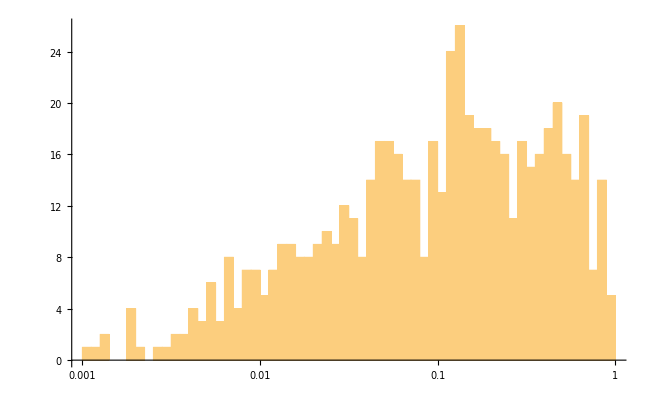

```mathematica
binMinComp=0.001;
binMaxComp=1;
binWidthLogComp=0.05;
binsComp=10^Range[Log[10,binMinComp],Log[10,binMaxComp],binWidthLogComp]
Histogram[Flatten[#[[2]]&/@comp1],{"Log",{binsComp}}]
```

### Functions

>>>Note assumes dist input,need to parameterize for distR01,etc.,or force the situation

```mathematica
distmeas[sample_,cutoff_, ioracc_Integer]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal},
dist = Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],comp1[[sample[[i]],2]].comp1[[sample[[j]],2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],0}],{i,1,Length@comp1},{j,1,Length@comp1}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]>cutoff&];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd];
distfinal = If[ioracc==0,distfd, distfds];
distfinal
]

distmeas1[sample_,cutoff_, ioracc_Integer,t_]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal},
dist = Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],trunc[comp1[[sample[[i]],2]],t].trunc[comp1[[sample[[j]],2]],t]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],0}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]>cutoff&];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd];
distfinal = If[ioracc==0,distfd, distfds];
distfinal
]

distmeasEu[sample_,cutoff1_, cutoff2_,oppnets_,ioracc_Integer]:=Module[{dist,distf,distfj,distff,distfs,distfd,distfds,distfinal,ONdistn},
(*cutoff1 is for top three topics. Cutoff 2 is for all topics*)
topThreeIX=Table[ToExpression[StringSplit[doctopics3[[sample[[i]],23]],":"]],{i,1,Length[sample]}];
topThreeComp=Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]], Sqrt[Total[(comp1[[sample[[i]],2]][[topThreeIX[[i]]]]-comp1[[sample[[j]],2]][[topThreeIX[[i]]]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
dist = Table[If[i<j&&topThreeComp[[i,j,3]]<cutoff1,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],Sqrt[Total[(comp1[[sample[[i]],2]]-comp1[[sample[[j]],2]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]<cutoff2&];
(*Find distances of OppNets to all, then look at ten with smallest distance*)
ONdist=Table[SortBy[Select[distfd,#[[1]]==oppnets[[i]]||#[[2]]==oppnets[[i]]&],Last],{i,1,Length[oppnets]}];
ONdist1=Table[Take[ONdist[[i]],If[Length[ONdist[[i]]]≥10,10,Length[ONdist[[i]]]]],{i,1,Length[oppnets]}];
(*Find non-OppNet Grants related to each OppNet {output grant ID, ApplID, Title, distance}*)
nonON = Table[Table[Flatten[{Complement[{ONdist1[[i,j,1]],ONdist1[[i,j,2]]},{oppnets[[i]]}],ONdist1[[i,j,3]]},1],{j,1,Length[ONdist1[[i]]]}],{i,1,Length[oppnets]}];
(*Create non-OppNet Lists WITH IX, ApplID, Tittle, distance based on Oppnets*)
lists0=Map[Style[StringJoin[ToString[doctopics3[[#,1]]],"-",ToString[doctopics3[[#,2]]],"-",doctopics3[[#,8]],"-",doctopics3[[#,19]]],Bold]&,oppnets];
lists1=Map[StringJoin[ToString[doctopics3[[#[[1]],1]]],"-",ToString[doctopics3[[#[[1]],2]]],"-",doctopics3[[#[[1]],8]],"-",doctopics3[[#[[1]],19]],"-",ToString[#[[2]]]]&,nonON,{2}];
lists2=If[Length[lists1]==Length[lists0],Table[Flatten[{lists0[[i]],lists1[[i]]}],{i,1,Length[lists0]}],{}];
distfd1=Map[{#[[1]],#[[2]],1/#[[3]]}&,distfd];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd1];
distfinal = If[ioracc==0,distfd1, distfds];
distfinal
]
distmeasEu1[sample_,cutoff1_, cutoff2_,ioracc_Integer]:=Module[{distTst,distf,distfj,distff,distfs,distfd,distfds,distfinal,ONdistn},
(*cutoff1 is for top three topics. Cutoff 2 is for all topics*)
topThreeIX=Table[ToExpression[StringSplit[doctopics3[[sample[[i]],topTopicsPos]],":"]],{i,1,Length[sample]}];
topThreeComp=Table[If[i<j,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]], Sqrt[Total[(comp1[[sample[[i]],2]][[topThreeIX[[i]]]]-comp1[[sample[[j]],2]][[topThreeIX[[i]]]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
dist = Table[If[i<j&&topThreeComp[[i,j,3]]<cutoff1,{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],Sqrt[Total[(comp1[[sample[[i]],2]]-comp1[[sample[[j]],2]])^2]]},{comp1[[sample[[i]],1]],comp1[[sample[[j]],1]],99}],{i,1,Length[sample]},{j,1,Length[sample]}];
distf =Flatten[dist,1];
distfd=Select[distf,#[[3]]<cutoff2&];
distfd1=Map[{#[[1]],#[[2]],If[#[[3]]≠0.,1/#[[3]],99]}&,distfd];
distfds=Map[{IXapplIDNEWassoc[[Key[#[[1]]]]],IXapplIDNEWassoc[[Key[#[[2]]]]],#[[3]]}&,distfd1];
distfinal = If[ioracc==0,distfd1, distfds];
distfinal
]
dist=distR01;
distcutoff[histCutoff_,distCutoff_,binWidth_]:=Module[{t,y,sing1},
sing={};
(*dist=distR01;*)
bc=Table[BinCounts[Map[#[[3]]&,dist[[t,y]]],binWidth],{t,1,25},{y,1,9}];
bcacc=Table[Accumulate[N[bc[[t,y]]/(If[Total[bc[[t,y]]]<1,AppendTo[sing,ToString[t]<>"-"<>ToString[y]];100+Total[bc[[t,y]]],Total[bc[[t,y]]]])]],{t,1,25},{y,1,9}];
bcaccix=Table[{i,bcacc[[t,y,i]]},{t,1,25},{y,1,9},{i,1,Length[bcacc[[t,y]]]}];
cutoff=Table[(Min[If[Select[bcaccix[[t,y]],#[[2]]>histCutoff&]=={},0,Map[#[[1]]&,Select[bcaccix[[t,y]],#[[2]]>histCutoff&]]]]*binWidth+distCutoff),{t,1,25},{y,1,9}];
cutoff
]
graphlabel=Table["Topic - "<>ToString[k]<>" - "<>ToString[2008-1+j],{k,1,25},{j,1,9}];
graphlabelR01=Table["R01 - Topic - "<>ToString[k]<>" - "<>ToString[2008-1+j],{k,1,25},{j,1,9}];
grfb[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,graphlabel_,vSpec_Integer]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
(*vertices2 =  Table[Tooltip[vertices[[i]],"Acc# - "<>ToString[IXapplIDNEWassoc[[Key[vertices[[i]]]]]]<>", State: "<>doctopics3[[vertices[[i]],20]]<>", Top Topics #: "<>"N/A"<>", \nTitle: "<>doctopics3[[vertices[[i]],8]]<>",\n"<>"Top Keywords: "<>"N/A"<>", RCDC: N/A"<>(*doctopics3[[vertices[[i]],8]]),*) ", Award: $"<>ToString[doctopics3[[vertices[[i]],14]]]<>",  Start-Year: "<>ToString[doctopics3[[vertices[[i]],7]]]],{i,1,Length[vertices]}];*)
(*inst={"MH","AA","DA","AG","HD","NS", "DC"};
instCode=Map[If[Or@@Table[#[[9]]==inst[[k]],{k,1,7}],Switch[#[[9]],"MH",Red,"AA",Blue, "DA",Yellow, "AG",Green, "HD",Magenta,"NS",Orange,"DC",Cyan],Gray]&,doctopics3];*)
inst={"AA","AG","CA","DA",  "HD", "HL","MH"};
instCode=Map[If[Or@@Table[#[[9]]==inst[[k]],{k,1,7}],Switch[#[[9]],"MH",Red,"AA",Blue, "DA",Yellow, "AG",Green, "HD",Magenta,"HL",Orange,"CA",Cyan],Gray]&,doctopics3];
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
grf=Graph[vertices,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,
VertexStyle->Table[vertices[[i]]->instCode[[vertices[[i]]]],{i,1,Length[vertices]}],
VertexLabels->If[lblflg==1,Table[vertices[[i]]->Style[doctopics3[[vertices[[i]],23]],8],{i,1,Length[vertices]}],None],
(*VertexStyle->Table[vertices[[i]]->ccstyle[[i]],{i,1,Length[vertices]}],VertexSize->{931->{0.1,0.2}},*)PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
grfTopics1[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,graphlabel_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCode},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],10];
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,10}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Yellow, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
verticesLBL={#[[1]],#[[2]]}&/@Map[doctopics3[[#]]&,vertices];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL[[j]]],{j,1,Length[vertices]}];
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->4,#[[1]]->2]&,bacYesNo];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],
PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
```

```mathematica
grfTopics2old[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,graphlabel_,vtex_,cond_, rfp_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCodeHld},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
(*The next line assigns color by highest to lowest occurring class*)
(*tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];*)
(*The next line assigns color by class number*)
tentopics=ToString[#]&/@Range[tnum];
(*not sure what next line is*)
(*tentopics=Join[tentopics,Range[tnum+1,10]];*)
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Yellow, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
colx=Gray;
(*topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],colx,tentopics[[2]],colx,tentopics[[3]],colx, tentopics[[4]],colx,tentopics[[5]],colx,tentopics[[6]],colx,tentopics[[7]],colx,tentopics[[8]],colx,tentopics[[9]],colx,tentopics[[10]],colx],colx]&,doctopics3];*)
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
verticesLBL={#[[1]],#[[2]],#[[3;;]]}&/@Map[doctopics3[[#]]&,vertices];
verticesLBL1=#[[2]]&/@Map[tk1[[#]]&,vertices];
verticesLBL1a=#[[2]]&/@Map[tk1graph[[#]]&,vertices];
verticesLBL2=Map[{md1[[#]], dataIX[[#]]}&,vertices];
verticesLBL3=Map[allTable2[[#]]&,vertices];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL3[[j]]],{j,1,Length[vertices]}](*version 2*);
verticesTT=Table[Tooltip[vertices[[j]],{verticesLBL[[j]],verticesLBL1[[j]],verticesLBL1a[[j]],verticesLBL2[[j]]}],{j,1,Length[vertices]}](*version 1*);
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->1]&,bacYesNo];
If[Length[vtex]>0,Goto[many]];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->3,#[[1]]->#[[2]]]&,vertexSize];
vertexSize=If[ToString[Head[vtex]]=="String",Map[If[StringTake[#[[4,allTabPos1]],2]==vtex,#[[1]]->2,#[[1]]->1]&,Map[allTable2[[#]]&,vertices]],vertexSize];
Label[many];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->1.5,#]&,vertexSize],vertexSize];
(*vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->2]&,bacYesNo];*)
diseaseShape1=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1]],#[[4,2]]}&,Map[allTable2[[#]]&,vertices]],#[[2]]==cond&]];
diseaseShape11=Map[#[[1]]->If[#[[1]]≥133,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
diseaseShape11=Map[#[[1]]->If[#[[4,allTabPos]]==cond,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape1,EdgeStyle->Lighter[Gray,0.25],PlotLabel->Style[graphlabel,18,Black,Bold]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape11,EdgeStyle->Lighter[Gray,0.25],PlotLabel->Style[graphlabel,14,Black,Bold]];
grf
]
```

>>>graph_code - CURRENT VERSION IN USE

```mathematica
grfTopics2[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,graphlabel_,vtex_,cond_, rfp_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopics,topicCodeHld},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]≠0&&#[[3]]<cutoffU&];
edgeWeights=If[#[[3]]≥0.5,50,1]&/@edges;
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
vlist=vertices; (*for output*)
Do[ixdataIX[dataIX[[i]]]=i,{i,1,Length@dataIX}];
(*The next line assigns color by highest to lowest occurring class*)
(*tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[#[[1]]&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];*)
(*The next line assigns color by class number*)
tentopics=ToString[#]&/@Range[tnum];
(*not sure what next line is*)
(*tentopics=Join[tentopics,Range[tnum+1,10]];*)
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Red,tentopics[[2]],Blue,tentopics[[3]],Orange, tentopics[[4]],Green,tentopics[[5]],Magenta,tentopics[[6]],Yellow,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3[[#]]&/@vertices];
colx=Gray;
(*topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,tnum}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],colx,tentopics[[2]],colx,tentopics[[3]],colx, tentopics[[4]],colx,tentopics[[5]],colx,tentopics[[6]],colx,tentopics[[7]],colx,tentopics[[8]],colx,tentopics[[9]],colx,tentopics[[10]],colx],colx]&,doctopics3];*)
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
verticesLBL={#[[1]],#[[2]],#[[3;;]]}&/@(doctopics3[[#]]&/@vertices);
verticesLBL1=#[[2]]&/@Map[tk1[[#]]&,dataIX[[#]]&/@vertices];
verticesLBL1a=#[[2]]&/@Map[tk1graph[[#]]&,dataIX[[#]]&/@vertices];
verticesLBL2=Map[{md1[[#]],tk2[[#,2]],tk2[[#,1]],subjIX[md1[[#,8]]]}&,dataIX[[#]]&/@vertices];
(*verticesLBL3=Map[allTable2[[#]]&,(ixdoctopics3[#]&/@vertices) ];*)
(*verticesTT=Table[Tooltip[vertices[[j]],verticesLBL3[[j]]],{j,1,Length[vertices]}]*)(*version 2*);
verticesTT=Table[Tooltip[vertices[[j]],{verticesLBL[[j]],verticesLBL1[[j]],verticesLBL1a[[j]],verticesLBL2[[j]]}],{j,1,Length[vertices]}](*version 1*);
bacYesNo=Map[{ixdataIX[#[[1]]],Or@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];
(*bacYesNo=Map[{ixdataIX[#[[1]]],And@@Table[IntersectingQ[#[[2]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk1[[#]]&,dataIX[[#]]&/@vertices]];*)
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->1]&,bacYesNo];
If[Length[vtex]>0,Goto[many]];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->3,#[[1]]->#[[2]]]&,vertexSize];
vertexSize=If[ToString[Head[vtex]]=="String",Map[If[StringTake[#[[4,allTabPos1]],2]==vtex,#[[1]]->2,#[[1]]->1]&,Map[allTable2[[#]]&,vertices]],vertexSize];
Label[many];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->1.5,#]&,vertexSize],vertexSize];
vertexSize=If[Length[vtex]>0,Map[If[MemberQ[vtex,#[[1]]],#[[1]]->2.1,#]&,vertexSize],vertexSize];
(*vertexSize=Map[If[#[[2]]==True,#[[1]]->2,#[[1]]->2]&,bacYesNo];*)
(*diseaseShape1=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1]],#[[4,2]]}&,Map[allTable2[[#]]&,vertices]],#[[2]]==cond&]];
diseaseShape11=Map[#[[1]]->If[#[[1]]≥133,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];*)
diseaseShape11=Map[#[[1]]->If[#[[4,allTabPos]]==cond,"Diamond","Circle"]&,Map[allTable2[[#]]&,vertices]];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->rfp,"EdgeWeighted"->True},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[i]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape11,EdgeStyle->Lighter[Gray,0.25],EdgeWeight->edgeWeights, PlotLabel->Style[graphlabel,14,Black,Bold]];
grf
]
```

```mathematica
Do[ixdoctopics3[doctopics3[[i,1]]]=i,{i,1,Length@doctopics3}]
```

```mathematica
Do[ixtk1graph[tk1graph[[i,1]]]=i,{i,1,Length@tk1graph}]
```

```mathematica
Do[ixallTable[allTable[[i,1,1]]]=i,{i,1,Length@allTable}]
```

```mathematica
Do[ixdataIX[dataIX[[i]]]=i,{i,1,Length@dataIX}]
```

```mathematica
ixdataIX[153]
```

ixdataIX[153]

```mathematica
grfTopics3[dist_,cutoffL_, cutoffU_,lblflg_,clvl_,tnum_,cond_,graphlabel_,vtex_]:=Module[{edgesn,edges3n,verticesn,vertices2n,grf,g1n,res,inst,instCode,sl,ccstyle,cc,tentopicsn,topicCode,vLength,rand},
edges = Select[dist,#[[3]]≥cutoffL&&#[[3]]   ≠0&&#[[3]]<cutoffU&];
edges3 = Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Length[edges]}];
vertices= VertexList[Graph[edges3]];
(*vLength=Length[vertices];
rand=RandomReal[{0,1},vLength];
vertices=#[[1]]&/@SortBy[Map[{vertices[[#]],rand[[#]]}&,Range[1,vLength]],Last];*)
vlist=vertices; (*for output*)
tentopics=Take[#[[1]]&/@Reverse@SortBy[Tally[Flatten[{#[[1]],#[[2]]}&/@StringSplit[#[[topTopicsPos]]&/@doctopics3,":"]]],Last],tnum];
tentopics=Join[tentopics,Range[tnum+1,10]];
topicCode=Map[If[Or@@Table[StringSplit[#[[topTopicsPos]],":"][[1]]==tentopics[[k]],{k,1,10}],Switch[StringSplit[#[[topTopicsPos]],":"][[1]],tentopics[[1]],Blue,tentopics[[2]],Red,tentopics[[3]],Magenta, tentopics[[4]],Yellow,tentopics[[5]],Green,tentopics[[6]],Orange,tentopics[[7]],Cyan,tentopics[[8]],LightRed,tentopics[[9]],LightGreen,tentopics[[10]],LightBlue],Gray]&,doctopics3];
tentopicsO=tentopics;
topicCodeO=topicCode;
g1=Graph[vertices,edges3];
cc=BetweennessCentrality[g1];
ccstyle=Map[If[#≥clvl,Red,Green]&,cc];
(*Edit, remove next line after I ge the +1 fixed in subsequent lines*)
(*tsts=metadata[[subjidTixmetadata[tkixTname[vertices[[i]]]]+1]];*)
metaIX=Table[If[ToString[Head[subjidTixmetadata[If[Head[tkixTname[vertices[[i]]]]==String,tkixTname[vertices[[i]]],"XXX"]]]]=="Integer",subjidTixmetadata[If[Head[tkixTname[vertices[[i]]]]==String,tkixTname[vertices[[i]]],"XXX"]],"NA"],{i,1,Length@vertices}];
condition=Map[If[metaIX[[#]]≠"NA", ToString[metadata[[metaIX[[#]]+1,3]]],"NA"]&,Range[1,Length[metaIX]]];
(*Edit*)
(*verticesLBL0={#[[1]],#[[2]]}&/@Map[doctopics3[[#]]&,vertices];*)
(*position of components needs to be parametered, posComp doesn't do it*)
verticesLBL0={#[[1,1]],#[[1,2]],#[[1,3]],#[[1,6;;10]],#[[2]]}&/@Map[doctopics5[[#]]&,vertices];
(*doctopics5 is not in vertex order next line is a problem*)
(*verticesLBL=Map[Join[verticesLBL0[[#]],{condition[[#]]},doctopics5[[#,3]]]&,Range[1,Length[vertices]]];*)
verticesLBL=Map[Join[verticesLBL0[[#]],{condition[[#]]}]&,Range[1,Length[vertices]]];
verticesTT=Table[Tooltip[vertices[[j]],verticesLBL[[j]]],{j,1,Length[vertices]}];
(*Eventually change to doctopics5 from tk2*)
bacYesNo=Map[{#[[1]],Or@@Table[IntersectingQ[#[[3]],{bacFlat[[i]]}],{i,1,Length@bacFlat}]}&,Map[tk2[[#]]&,vertices]];
(*bacYesNo=Map[IntersectingQ[{#},mycoplasmaIX]&,vlist];*)
(*diseaseShape=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1,1]],#[[1,5]]}&,Map[doctopics5[[#]]&,vertices]],#[[2]]==cond&]];*)
diseaseShape=Map[#[[1]]->"Diamond"&,Select[Map[{#[[1,1]],#[[1,5]]}&,Map[doctopics5[[#]]&,vertices]],IntersectingQ[StringSplit[#[[2]],":"],{cond}]&]];
vertexSize=Map[If[#[[2]]==True,#[[1]]->3.0,#[[1]]->1.5]&,bacYesNo];
vertexSize=Map[If[#[[1]]==vtex,#[[1]]->6,#[[1]]->#[[2]]]&,vertexSize];
grf=Graph[verticesTT,edges3,GraphLayout->{"SpringElectricalEmbedding", "RepulsiveForcePower"->-1.6},ImageSize->Large,VertexSize->vertexSize,VertexStyle->Table[vertices[[i]]->topicCode[[vertices[[i]]]],{i,1,Length[vertices]}],VertexShapeFunction->diseaseShape,PlotLabel->Style[graphlabel,18,Black,Bold]];
grf
]
```

### Tooltip Data Construction

>>> The following are used in tooltips. You have the option of alphabetically sorting the objects or reverse sorting by abundance interval. Pick one only.

>>> Alphabetic sorts microbes within record, not records

```mathematica
tk1={#[[1]],Sort[#[[2]]]}&/@tk1;
```

>>>>Reverse abundance interval sort within record

```mathematica
tk1={#[[1]],Reverse@(SortBy[#[[2]],ToExpression[Last[StringSplit[#,"-"]]]&])}&/@tk1;
Length@%
```

123

```mathematica
SetDirectory["/Users/jeffreylapides/Documents/Mathematica_new/alzheimers/new_processing_AR_NW"];
```

>>> The following loads the raw abundance data. You will have to create your own file if you want this in the >>> tooltip or you can leave it out. You will need to edit it out of the variables below and replace it with a blank >>> list. It is not used in any computation, it is just informational in the tooltip.
>>> One record is displayed so that you can see the file format.

```mathematica
abunHyb=Import["data_norm_hybrid_only_AK_v2.csv","CSV"];
Length@%
```

124

```mathematica
abunHyb[[1]];
```

```mathematica
abunHyb[[2]]
```

{2016P1_lbc10,92.9203,0.,0.,0.,0.,0.,0.,0.147493,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.884956,0.,0.,0.,0.,0.,6.0472,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
abunHyb1=number[abunHyb[[1]]];
```

```mathematica
Do[abunHybNameTIX[abunHyb1[[i,2]]]=abunHyb1[[i,1]],{i,1,Length@abunHyb1}]
```

```mathematica
abunHyb1[[3,2]]
```

Comamonas_jiangduensis

```mathematica
abunHybNameTIX["Comamonas_jiangduensis"]
```

3

```mathematica
abunHybNameTIX["Acinetobacter_junii"]
```

13

```mathematica
abunHybNameTIX["Propionibacterium_acnes"]
```

2

### Integrated input and result data for query analysis

>>> The following tables are various versions of integrated input and result data. They can be used in tooltips as well. Currently allTable2 is being used in the tooltip display.  They are also very useful for doing analysis with queries.
>>> An example of allTable 7 is stored on GitHub as well as with the paper.

```mathematica
allTable=Table[{doctopics3[[i]],md1[[dataIX[[i]]]],tk1[[dataIX[[i]]]],dataIX[[i]],datatest[[dataIX[[i]]]]},{i,1,Length@doctopics3}];
Length@%
allTable2=Map[{#[[1,1]],StringSplit[#[[1,2]],":"][[1]],#[[1,2]],#[[2]],#[[4]],RandomChoice[{0.5,0.5}->{"AD","C"}]}&,allTable];
Length@%
allTable4=Map[{Flatten@{#[[1,1]],StringSplit[#[[1,2]],":"][[1]],#[[1,2]],#[[1,3;;numTopics+2]]},{#[[2,1]],#[[2,2]],#[[2,3]],Switch[StringTake[#[[2,6]],2],"AD","AK","NW","NW"],#[[2,8]]},{#[[3,1]],#[[3,2]]},#[[4]],#[[5]]}&,allTable];
Length@%
allTable6=Table[{doctopics3[[i]],md1[[dataIX[[i]]]],tk1[[dataIX[[i]]]],dataIX[[i]],datatest[[dataIX[[i]]]],tk1graph[[dataIX[[i]]]]},{i,1,Length@doctopics3}];
Length@%
allTable7=FlattenAt[#,7]&/@Table[{Flatten@{doctopics3[[i,1]],StringSplit[doctopics3[[i,2]],":"][[1]],doctopics3[[i,2;;]]},md1[[dataIX[[i]]]],tk1[[dataIX[[i]]]],dataIX[[i]],datatest[[dataIX[[i]]]],tk1graph[[dataIX[[i]]]],Select[abunHyb,#[[1]]==md1[[dataIX[[i]],1]]&],subjIX[md1[[dataIX[[i]],8]]]},{i,1,Length@doctopics3}];
Length@allTable7
```

122

122

122

«2 more identical outputs»

>>> Here is an example from the paper that computes the occurrence of components in the samples from the data in allTable7.

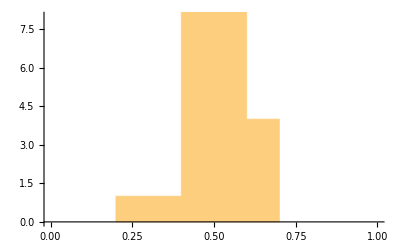
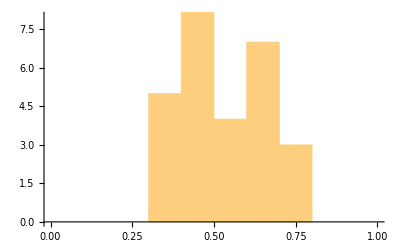
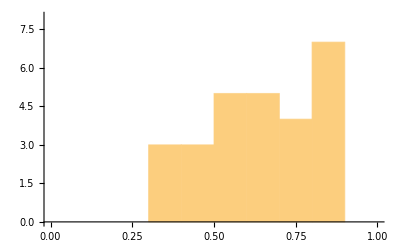
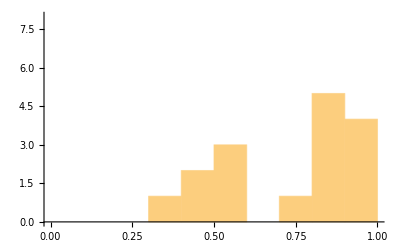
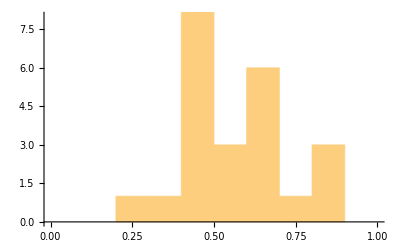

```mathematica
Table[Histogram[Flatten[#[[1,3+i]]&/@Select[allTable7,ToExpression[#[[1,2]]]==i&]],{0.1},PlotRange->{{0.,1.},{0,8}}],{i,1,5}]
```

>>> ENTER SOMETHING HERE

```mathematica
subjLst=Table[#[[1,1]]&/@Select[allTable7,#[[8]]==i&],{i,1,Length[subjSample1]}];
```

### Node Distance Setup

>>> distSimp is the pairwise similarity computed by multiplying sample components and summing.

```mathematica
dcutoff=0.05;
samp=#[[1]]&/@doctopics3;
sampLength=Length[samp]
distSimp=distmeas[samp,0.11,0];
Length@%
```

122

5407

>>> It is a good idea to record the length of distSimp to make sure multiple runs yield the same length. Small errors earlier in the pipeline can change number so this is a good check to make sure you did not forget to execute something or change a value.

>>>distSimp from previous run:

>>> The histogram below is also a good check to make sure nothing changed.

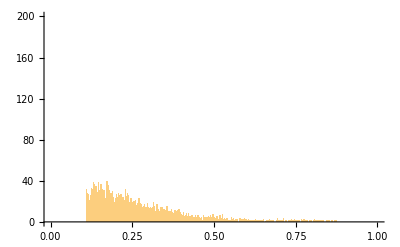

```mathematica
hist=Histogram[#[[3]]&/@distSimp,{0.001},PlotRange->{{0.0,1.0},{0,200}}]
```

### Graph

```mathematica
topicnum
```

5

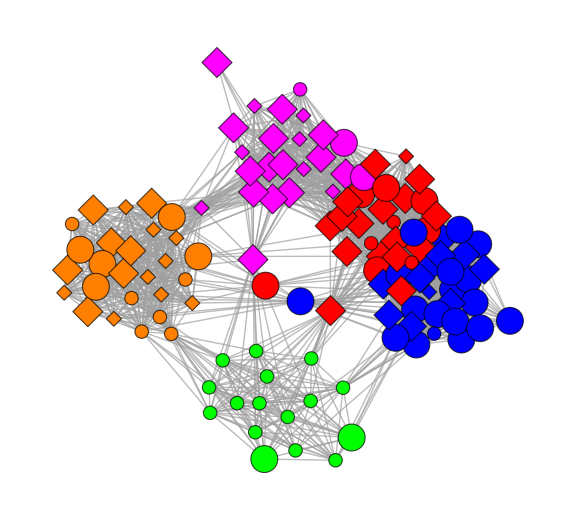

122

```mathematica
(*Title construction information, Use if you wish. Not required*)
(*title variable needs to be placed in grfTopics2 position 7 if you use it*)
name1="Alzheimer's- AK - Run 12.15 NW Staph removal, \n Hybrid Genus/Species; Collapsed Lo Count Hi Abun, \n mu/nu: 0.98, burnin-in: 99, mixing: 149";
cond="AD";
iterations=1000;
bacFlat1="";
wordcutoff1=1;
gcutoff=0.259;  (*similarity cutoff in histogram above, edges are formed for values above this value. Recorded in title*)
title=name1<>"\n"<>"Iterations: "<>ToString[iterations]<>", "<>", "<>"wordcutoff: "<>ToString[wordcutoff1]<>"\n"<>"dcutoff: "<>ToString[dcutoff]<>", "<>"gcutoff: "<>ToString[gcutoff]<>"\n"<>"Nodes enlarged for: "<>bacFlat1<>"\n"<>"Diamonds: "<>cond;
allTabPos=2;
allTabPos1=7;
(*bacFlat is the variable to use to enlarge nodes that contain any object in the list. You can see example with one or many objects. Since this code is not a function, you may find it useful to use a variable list you have computed. You can also set it equal to a blank string for no node enlargement*)
bacFlat={"Acinetobacter_junii-14"};
bacFlat={"Comamonas_jiangduensis-7","Comamonas_jiangduensis-8","Comamonas_jiangduensis-9","Comamonas_jiangduensis-10","Comamonas_jiangduensis-11","Comamonas_jiangduensis-12"};
bacFlat="";
bacFlat={"Propionibacterium_acnes-12","Propionibacterium_acnes-13","Propionibacterium_acnes-14"};
gg14=grfTopics2[distSimp,gcutoff,1.0,0,0,topicnum,"",1000,cond,-1.8]
Length[vertices]
```

## Analysis

>>> You can use, for example, allTable 7 to query the results.
>>> If you have not constructed the table above, you can load it here

```mathematica
allTable7tst=ToExpression[Import["allTable7.tsv","TSV"]];
```

```mathematica
allTable7tst[[1]]
```

{{1,2,2:1:5,0.296703,0.48489,0.00412088,0.00412088,0.210165},{2016P1_lbc10,C,frontal,01-55,01-55-F,ADJ1,ADJ1,uams_S22},{1,{Propionibacterium_acnes-14,Veillonella-9,Klebsiella-10,Streptococcus-12}},1,{1,{Propionibacterium_acnes-14,Veillonella-9,Klebsiella-10,Streptococcus-12}},{1,{Propionibacterium_acnes-14,Streptococcus-hi}},{2016P1_lbc10,92.9203,0.,0.,0.,0.,0.,0.,0.147493,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.884956,0.,0.,0.,0.,0.,6.0472,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},15}

>>> allTable7 1st element: index, top class, top three classes, class components
>>> allTable7 2nd element: sample id, disease, location, user def, user def, user def, user def, subject id
>>> allTable7 3rd element:: index, object list with original bins, 
>>> allTable7 4th element: index
>>> allTable7 5th element:  index, object list with original bins, 
>>> allTable7 6th element: index, filtered object list with hi-low bins for some objects
>>> allTable7 7th element: sample id, normalized abundances of microbes
>>> allTable7 8th element: subject index